# Hexi—PS20—2025 - 04 - 22

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

### Exercises from EIWL3 Section 45

```mathematica
planets=CloudGet["https://wolfr.am/7FxLgPm5"]
```

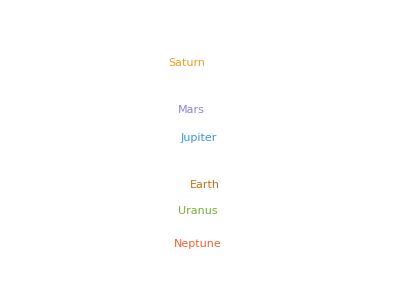

```mathematica
Normal[planets[All,"Moons",Length]]//WordCloud
```

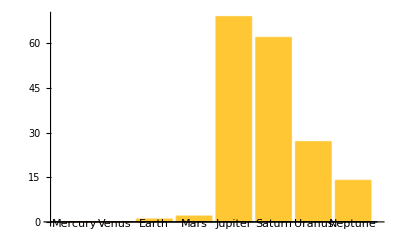

```mathematica
BarChart[Normal[planets[All,"Moons",Length]],ChartLabels->Automatic]
```

```mathematica
planets[SortBy[Length[#Moons]&],"Mass"]
```

```mathematica
planets[All,"Moons",Max,"Mass"]
```

```mathematica
Sort[planets[All,"Moons",Total,"Mass"]]
```

```mathematica
planets[All,"Moons",Median,"Mass"]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.0001, "EarthMass"]&]][All,Keys]
```

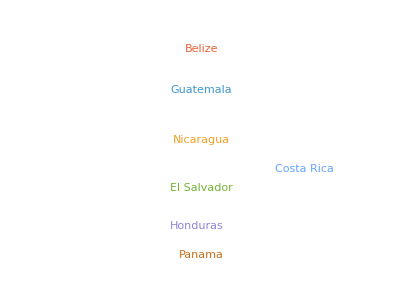

```mathematica
countries=EntityClass["Country","CentralAmerica"]["Name"];
lengths=StringLength[WikipediaData[#]]&/@countries;
countriesdata=AssociationThread[countries->lengths];
WordCloud[countriesdata]
```

```mathematica
fireballs=ResourceData["Fireballs and Bolides"];
fireballs[Max,"Altitude"]
```

66.6 km

```mathematica
Take[ReverseSort[fireballs[All,"Altitude"]],5]
```

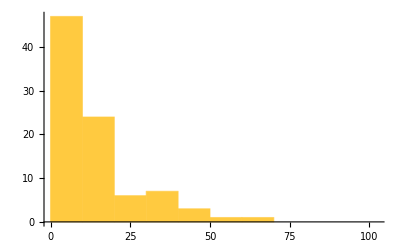

```mathematica
Differences[fireballs[All,"PeakBrightness"]]//Histogram
```

```mathematica
GeoListPlot[Take[fireballs,{1,10}][All,"NearestCity"],GeoLabels->True]
```

-Graphics-

```mathematica
GeoListPlot[fireballs[TakeLargestBy[#Altitude&,10],"NearestCity"],GeoLabels->True]
```

-Graphics-

### Exercises from EIWL3 Section 46

```mathematica
Spectrogram[SpeechSynthesize[IntegerName[123456]]]
```

-Graphics-

```mathematica
Spectrogram[SpeechSynthesize[ReverseSortBy[WordList[],StringLength][[1]]]]
```

-Graphics-

```mathematica
SpeechSynthesize[StringRiffle[Alphabet[],Nothing]]
```

```mathematica
StringRiffle[Alphabet[],Nothing]
```

{a, b, c, d, e, f, g, h, i, j, k, l, m, n, o, p, q, r, s, t, u, v, w, x, y, z}

```mathematica
AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
Table[SpeechRecognize[AudioPitchShift[SpeechSynthesize["computer"],n]],{n,1,1.5,0.1}]
```

{computer,computer,computer,come pure day,compure day,comple}

```mathematica
(*Sound[SoundNote[#,1,"Guitar"]&/@{0,12,24}]//AudioPlot.This does not work on my laptop.*)
```

```mathematica
(*Table[AudioPitchShift[Sound[SoundNote[0,1,"Trumpet"]],n],{n,0.5,1,0.1}]//AudioIdentify This does not work on my laptop.*)
```

```mathematica
AnimationVideo[Blur[CurrentImage[],n],{n,20,0}]
```

```mathematica
AnimationVideo[Graphics[{RegularPolygon[n],Circle[]}],{n,3,20}]
```

```mathematica
AnimationVideo[Graphics[{Hue[n],Disk[],ImageSize->50}],{n,0,1}]
```

```mathematica
AnimationVideo[Rasterize[ToUpperCase[FromLetterNumber[n]],RasterSize->200],{n,1,26,1}]
```